# Math Boot Camp: Div, Grad, Curl

You can skip this boot camp if you can answer the following question:

Example
Calculate the divergence of the vector field A⃗= x̂+ŷ. Does the answer make sense?

Example
Calculate the curl of the vector field A⃗= -y x̂+x ŷ. Do you expect the answer to be zero or nonzero?

### Position

The position vector r⃗ is defined as

r⃗=x x̂+y ŷ+z ẑ

with norm

r=(x^2+y^2+z^2)^(1/2)

The corresponding unit vector (pointing radially outwards) equals

r̂=(r⃗)/r=(x x̂+y ŷ+z ẑ)/((x^2+y^2+z^2)^(1/2))

We define the infinitesimal displacement vector from the point (x,y,z) to the point (x+ⅆx,y+ⅆy,z+ⅆz) as

ⅆ s⃗=ⅆx x̂+ⅆy ŷ+ⅆz ẑ

(We could call this ⅆ r⃗, since that is what it is, but it is useful to reserve a special letter for infinitesimal displacements.)

### Derivatives

Given a function of one variable f[x], its derivative ⅆf tells us the rate of change of f,

ⅆf=(ⅆf/ⅆx)ⅆx

In other words, if we change x by an amount ⅆx, then f will change by an amount ⅆf, with the derivative being the proportionality factor. This has a nice geometrical interpretation as the slope of the function f[x].

A function of 3 variables T[x,y,z] requires us to generalize our definition of the derivative to

ⅆT=((∂T)/(∂x))ⅆx+((∂T)/(∂y))ⅆy+((∂T)/(∂z))ⅆz

where the notation (∂T)/(∂x) is the partial derivative of T with respect to x (which means that y and z are treated as constants when taking this derivative (for example, if T=2 x^2 y then (∂T)/(∂x)=4x y, (∂T)/(∂y)=2 x^2, and (∂T)/(∂z)=0)). We could write this equation more compactly as

ⅆT=OverVector[∇]T·ⅆ s⃗

where

OverVector[∇]T≡(∂T)/(∂x)x̂+(∂T)/(∂y)ŷ+(∂T)/(∂z)ẑ

is the gradient of T (i.e. the 3D analog of the derivative) and

ⅆ s⃗=ⅆx x̂+ⅆy ŷ+ⅆz ẑ

is the infinitesimal displacement vector from above. Using a property of the dot product,

ⅆT=|OverVector[∇]T||ⅆ s⃗|Cos[θ]

where θ is the angle between the vectors OverVector[∇]T and ⅆ s⃗. So if we fix the magnitude |ⅆ s⃗| and rotate it around to cover all possible directions, then the maximum change in ⅆT will occur when θ=0 (which implies that ⅆ s⃗ points in the same direction as OverVector[∇]T). Therefore, a geometric interpretation of the gradient is that

OverVector[∇]T points in the direction of maximum increase of the function T

and furthermore that

|OverVector[∇]T| gives the slope of T along this maximal direction

Using the above expression, we also immediately see that -OverVector[∇]T is the direction of maximum decrease of the function T, and that any direction perpendicular to OverVector[∇]T will result is no change to T (i.e. this plane will have a constant T value). Of course, all of these statements only hold for an infinitesimal displacement ⅆ s⃗.

We can write

OverVector[∇]T=(∂T)/(∂x)x̂+(∂T)/(∂y)ŷ+(∂T)/(∂z)ẑ
=(x̂∂/(∂x)+ŷ∂/(∂y)+ẑ∂/(∂z))T

where

OverVector[∇]=x̂∂/(∂x)+ŷ∂/(∂y)+ẑ∂/(∂z)

is the del operator. Note that the derivatives in OverVector[∇] each act separately on T. Also, because the unit vectors never change magnitude or direction (i.e. (∂x̂)/(∂x)=0), you typically see OverVector[∇] written as OverVector[∇]=∂/(∂x)x̂+∂/(∂y)ŷ+∂/(∂z)ẑ, which is how I will write it throughout the rest of the notes.

Note that OverVector[∇] is not a normal vector, but instead an operator that acts upon a scalar to produce a vector (so OverVector[∇]T does not mean ordinary multiplication). In fact, we know of three ways that vectors can be multiplied:

Multiply vector A⃗ by a scalar c: c A⃗

Take the dot product of two vectors A⃗ and B⃗: A⃗·B⃗

Take the cross product of two vectors A⃗ and B⃗: A⃗×B⃗

Correspondingly, the OverVector[∇] operator can act in three ways:

On a scalar function T: OverVector[∇]T (the gradient of T)

On a vector A⃗ via the dot product: OverVector[∇]·A⃗ (the divergence of A⃗)

On a vector A⃗ via the cross product: OverVector[∇]×A⃗ (the curl of A⃗)

We already discussed the gradient above, so we now focus on the last two operations.

### Divergence

The divergence of a vector A⃗=A_x x̂+A_y ŷ+A_z ẑ equals

OverVector[∇]·A⃗=(∂/(∂x)x̂+∂/(∂y)ŷ+∂/(∂z)ẑ)·(A_x x̂+A_y ŷ+A_z ẑ)
=(∂A_x)/(∂x)+(∂A_y)/(∂y)+(∂A_z)/(∂z)

Note that the divergence of a vector is a scalar (and there is no such thing as the divergence of a scalar)! Geometrically, the divergence of a vector A⃗ represents how much A⃗ spreads out from any point. More precisely, if you treat A⃗ as describing the flow of a fluid and you put an infinitesimally small volume at a point r⃗, then the volume will empty out in time if the divergence is positive, fill up with time if the divergence is negative, and hold the same amount of fluid if the divergence equals zero. In other words, the divergence measures the "amount of arrow" leaving an infinitesimal volume at each point in space, with larger arrows counting more than smaller arrows.

An Important Point: In this course, we will often work with vectors which are themselves functions of position. For example, A⃗=x x̂+y ŷ is a different vector at each point and space (and it has a positive divergence equal to 2 at each point in space). We can sample different points in space to get a feel for what this looks like, as shown below. These "vectors" are actually called vector fields.

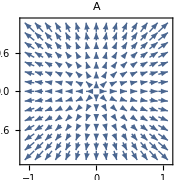

```mathematica
centerPlot@VectorPlot[{x,y},{x,-1,1},{y,-1,1},ImageSize->Small,PlotLabel->"A"]
```

Example
Calculate the divergence of the vector field A⃗= x̂+ŷ. Does the answer make sense?

Solution
Since this is a constant vector field, the amount of arrows entering any infinitesimal volume equals the number of arrows exiting that volume.

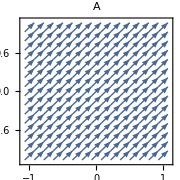

```mathematica
centerPlot@VectorPlot[{1,1},{x,-1,1},{y,-1,1},ImageSize->Small,PlotLabel->"A"]
```

And indeed, OverVector[∇]·A⃗=∂/(∂x)[1]+∂/(∂y)[1]=0, as expected. □

Example
Calculate the divergence of the vector field A⃗=x x̂+y^2 ŷ.

Solution
Plugging into our equation, OverVector[∇]·A⃗=(∂x)/(∂x)+(∂y^2)/(∂y)=1+2y. But let’s visually check this by plotting the 3D vector field.

```mathematica
centerPlot@VectorPlot3D[{x,y^2,0},{x,-1,1},{y,-1,1},{z,-1,1},ImageSize->Small,PlotLabel->"A",VectorStyle->Arrowheads[0.03]]
```

-Graphics3D-

This plot - while correct - is extremely cluttered. Because A⃗ does not depend upon z, we can simply take a cut of this vector field at z=0.

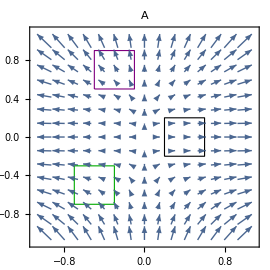

```mathematica
p1={0.4,0.};p2={-0.5,-0.5};p3={-0.3,0.7};r=0.2;
centerPlot@Show[VectorPlot[{x,y^2},{x,-1,1},{y,-1,1},ImageSize->270,PlotLabel->"A"],Graphics[{FaceForm[],EdgeForm[Black],Rectangle[p1+{-r,-r},p1+{r,r}],EdgeForm[Darker@Green],Rectangle[p2+{-r,-r},p2+{r,r}],EdgeForm[Purple],Rectangle[p3+{-r,-r},p3+{r,r}]}]]
```

Consider the point (0.4,0) shown by the black square above. There are no vectors going in or out of it in the y-direction, but there are definitely larger vectors coming out of the square than going into it. This signifies that there will be positive divergence, in line with the result (1+2y)_(x=0.4,y=0)=1 found above. Similarly, the green square around (-0.5,-0.5) has larger vectors entering it than leaving it on the top and bottom and larger vectors leaving it than entering it on its sides. These two effects seem rather equal, and indeed we find (1+2y)_(x=-0.5,y=-0.5)=0 from above. Lastly, the purple square centered at (-0.3,0.7) has divergence (1+2y)_(x=-0.3,y=0.7)=2.4 which agrees with the fact that larger arrows are leaving the square than entering it. This shows the geometrical description of the divergence, but be warned: you must use an infinitesimal squares for this to be correct (I only showed a large square here for convenience!) □

Example
Compute the divergence of the vector field A⃗=(r̂)/r^2.

Solution
Recall that r⃗=⟨x,y,z⟩, so that r^2=x^2+y^2+z^2 and r̂=⟨x,y,z⟩/((x^2+y^2+z^2)^(1/2)). So in Cartesian coordinates,

A⃗=⟨x/((x^2+y^2+z^2)^(3/2)),y/((x^2+y^2+z^2)^(3/2)),z/((x^2+y^2+z^2)^(3/2))⟩

Therefore,

OverVector[∇]·A⃗=∂/(∂x)[x/((x^2+y^2+z^2)^(3/2))]+∂/(∂y)[y/((x^2+y^2+z^2)^(3/2))]+∂/(∂z)[z/((x^2+y^2+z^2)^(3/2))]

Computing the first of these terms,

∂/(∂x)[x/((x^2+y^2+z^2)^(3/2))]=1/((x^2+y^2+z^2)^(3/2))-(3 x^2)/((x^2+y^2+z^2)^(5/2))
=(-2 x^2+y^2+z^2)/((x^2+y^2+z^2)^(5/2))

By symmetry (i.e. by redefining x→y, y→z, and z→x), the other two terms must be

∂/(∂y)[y/((x^2+y^2+z^2)^(3/2))]=(x^2-2 y^2+z^2)/((x^2+y^2+z^2)^(5/2))

∂/(∂z)[z/((x^2+y^2+z^2)^(3/2))]=(x^2+y^2-2 z^2)/((x^2+y^2+z^2)^(5/2))

and therefore

OverVector[∇]·A⃗=0

That is pretty shocking, for if we draw this vector field (taking a cut at z=0), what do we expect for its divergence to be?

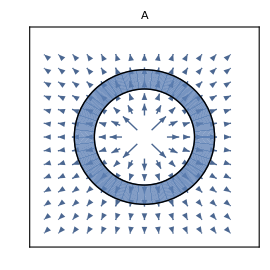

```mathematica
centerPlot@Show[VectorPlot[{x,y}/Max[(x^2+y^2)^(3/2),10^-5],{x,-0.1,0.1},{y,-0.1,0.1},ImageSize->270,PlotLabel->"A",FrameTicks->False,RegionFunction->Function[{x,y},0.02<(x^2+y^2)^(1/2)]],ParametricPlot[{r Cos[θ],r Sin[θ]},{r,0.05,0.07},{θ,0,2π}],Graphics[{Circle[{0,0},0.05],Circle[{0,0},0.07]}]]
```

But upon closer inspection, maybe this isn’t so crazy. Let’s consider the area between a circle of radius r_1 and r_2 where r_1<r_2. Note that the divergence represents the amount of the arrows leaving an infinitesimal volume at each point in space, and not on a finitely large circle. However in the special case where the divergence equals 0 everywhere, that means that at each infinitesimal volume in space, the amount of arrows leaving that point equal the amount of arrows entering it, so in this case only the amount of arrows entering a finite volume should equal the amount of arrows leaving a finite volume. Let’s check this for the donut shown above.

The arrows enter the donut all along its inner perimeter, which has length 2π r_1, and these arrows have magnitude 1/r_1^2. Therefore, the cumulative effect of all these arrows on the inner perimeter equals (2π r_1)(1/r_1^2)=(2π)/r_1. Similarly, the arrows leaving the donut occur at the perimeter 2π r_2 with magnitude 1/r_2^2. Therefore, the weight of these arrows equals (2π r_2)(1/r_2^2)=(2π)/r_2. So we expect that the divergence, which equals the weight of the arrows leaving the figure minus the weight of the arrows entering the figure, should equal (2π)/r_2-(2π)/r_1. Since r_1<r_2, this is a negative number, and certainly not zero. So what went wrong?

The problem is that we are working in 2D, rather than 3D! Indeed, in 2D the divergence is negative (in fact, it is -1/r^3), but in 3D we have to take into account the surface area of the inner and outer spheres. Therefore, he weight of the arrows entering the inner sphere equals (4π r_1^2)(1/r_1^2)=4π while the weight of the arrows leaving the outer sphere equals (4π r_2^2)(1/r_2^2)=4π, and these two contributions do indeed cancel to leave a net 0 divergence!

Great, but we still have one more mystery to solve. While it may seem reasonable that the divergence of A⃗=(r̂)/r^2 is 0 at every point, there is one point at which this cannot be so: the origin. For at the origin, there are vectors emanating outwards in every direction, so putting an infinitesimal sphere at the origin must surely yield a positive divergence. In fact, as it turns out, the divergence at the origin is infinitely large, and later in the course we will quantify this infinity explicitly to determine the electric potential from a point charge.

### Curl

We now turn to the final operation you can do with the OverVector[∇] operator, namely, taking the curl of a vector A⃗=A_x x̂+A_y ŷ+A_z ẑ, which equals

OverVector[∇]×A⃗=|x̂ | ŷ | ẑ
∂/(∂x) | ∂/(∂y) | ∂/(∂z)
A_x | A_y | A_z|
=((∂A_z)/(∂y)-(∂A_y)/(∂z))x̂+((∂A_x)/(∂z)-(∂A_z)/(∂x))ŷ+((∂A_y)/(∂x)-(∂A_x)/(∂y))ẑ

Note that the curl of a vector yields another vector. You cannot take the curl of a scalar, or a 1D or 2D vector. Therefore, when taking the curl of a vector such as A⃗= x̂+ŷ we will always assume it is a 3D vector with zero for its ẑ component.

The curl measures how much a vector field "curves around" a point. If an object in your vector field would rotate (ignore its translation and just focus on rotation) then that point has a non-zero curl. For example, considering the motion of water in a pond, a whirlpool would be a region of large curl with the direction of the curl given by the right-hand rule (i.e. when you wrap your fingers in the direction of the rotation, your thumb points in the direction of the curl).

Example
Calculate the curl of the vector field A⃗= -y x̂+x ŷ. Do you expect the answer to be zero or nonzero?

Solution
We expect from the shape of the vector field that there will be a curl in the +ẑ direction.

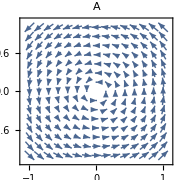

```mathematica
centerPlot@VectorPlot[{-y,x},{x,-1,1},{y,-1,1},ImageSize->Small,PlotLabel->"A"]
```

And indeed, OverVector[∇]×A⃗=((∂A_z)/(∂y)-(∂A_y)/(∂z))x̂+((∂A_x)/(∂z)-(∂A_z)/(∂x))ŷ+((∂A_y)/(∂x)-(∂A_x)/(∂y))ẑ=2 ẑ. This may perhaps seem like an obvious statement about the origin, but the result means more than that, since OverVector[∇]×A⃗=2 ẑ implies that placing a small object at any point will result in that object rotating at the same rate (although for any point that isn’t the origin the object will also translate). □

Example
Calculate the curl of the vector field A⃗= x x̂+y ŷ+z ẑ.

Solution
This vector field points radially outward. What do we expect the curl to be?

```mathematica
centerPlot@VectorPlot3D[{x,y,z},{x,-1,1},{y,-1,1},{z,-1,1},ImageSize->Small,PlotLabel->"A"]
```

-Graphics3D-

From our formula, OverVector[∇]×A⃗=0. Does this make sense? Looking at the plane z=0,

```mathematica
centerPlot@VectorPlot[{x,y},{x,-1,1},{y,-1,1},ImageSize->Small,PlotLabel->"A"]
```

-Graphics-

we see that although any small object would certainly be pushed radially outwards, it will not rotate. For example, placing a sphere - which in the z=0 plane is a circle - at the point (0,1) shows that the rotation on the points in the left side of the sphere will be perfectly balanced by the rotation on the points in the right side of the sphere. Because the sphere will not rotate, its curl must be zero. This applies to a circle at any other point by the symmetry of the vector field. □

## Mathematica Initialization

```mathematica
Clear[font]
font[text_,size_Integer:14,opts___]:=(Style[text,size,FontFamily->"Times",opts])
```